Министерство образования и науки Российской Федерации
Федеральное государственное бюджетное образовательное учреждение
высшего профессионального образования
«Национальный исследовательский Томский политехнический университет»

Институт: ИЯТШ
Отделение прикладной математики и информатики

ОТЧЕТ ПО ЛАБОРАТОРНОЙ РАБОТЕ №7
Классические ортогональные полиномы 
Вариант №2

Выполнил: студент группы 0В01 
Белясов Архип.
Проверил: Богданов О.В.

Томск 2023

Зададим кусочную функцию

```mathematica
f[x_]:=Piecewise[{{-1/5,-1<x<0},{BesselI[1,x]*Cos[x/2],0<=x<1}}];
```

Пункт А
	 Разложим данную функцию в ряд по полиномам Лежандра для x ∈ [−1, 1] , построить на одном графике предложенную функцию и ее n-частичные суммы с n=1, 2,…,5,… . Подобрать такое n-оптимальное ,чтобы максимальное отклонение n-частичные суммы от данной функции не превышало ϵ = 10% от |sup[f(x)]-inf[f(x)]| для любого x ∈ [−1, 1] .

```mathematica
ak[k_]:=(2 k +1)/2*NIntegrate[f[x]*LegendreP[k,x],{x,-1,1}];
fun[n_]:=Sum[ak[m]*LegendreP[m,x],{m,0,n}];
```

```mathematica
error = Abs[(MaxValue[{f[x], 0<x<=1},x]-MinValue[{f[x],-1<x<0},x])]*0.1;
```

Определим оптимальное количество n

```mathematica
iter = 1;
current = Max[Maximize[{fun[iter]-f[x],-1<x<-0.01},x][[1]],Maximize[{fun[iter]-f[x],0.01<x<1},x][[1]]];
While[current>error,
iter+=1;
current = Max[MaxValue[{fun[iter]-f[x], -1<x<-0.01},x],MaxValue[{fun[iter]-f[x], 0.01<x<1},x]];
Print["n = ", iter, ". Максимальное отклонение при заданном n = ", current];
If[iter ==54,Break[]]
];
```

n = 2. Максимальное отклонение при заданном n = 0.579016

n = 3. Максимальное отклонение при заданном n = 0.14177

n = 4. Максимальное отклонение при заданном n = 0.123996

n = 5. Максимальное отклонение при заданном n = 0.122713

n = 6. Максимальное отклонение при заданном n = 0.536987

n = 7. Максимальное отклонение при заданном n = 0.113537

n = 8. Максимальное отклонение при заданном n = 0.109015

n = 9. Максимальное отклонение при заданном n = 0.107738

n = 10. Максимальное отклонение при заданном n = 0.104811

n = 11. Максимальное отклонение при заданном n = 0.103537

n = 12. Максимальное отклонение при заданном n = 0.101488

n = 13. Максимальное отклонение при заданном n = 0.100216

n = 14. Максимальное отклонение при заданном n = 0.0987022

n = 15. Максимальное отклонение при заданном n = 0.0974321

n = 16. Максимальное отклонение при заданном n = 0.0962697

n = 17. Максимальное отклонение при заданном n = 0.0950013

n = 18. Максимальное отклонение при заданном n = 0.0940814

n = 19. Максимальное отклонение при заданном n = 0.092815

n = 20. Максимальное отклонение при заданном n = 0.0920696

n = 21. Максимальное отклонение при заданном n = 0.0908051

n = 22. Максимальное отклонение при заданном n = 0.0901896

n = 23. Максимальное отклонение при заданном n = 0.0889271

n = 24. Максимальное отклонение при заданном n = 0.0884109

n = 25. Максимальное отклонение при заданном n = 0.0871506

n = 26. Максимальное отклонение при заданном n = 0.0867118

n = 27. Максимальное отклонение при заданном n = 0.0854539

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.933578}. NIntegrate obtained -0.0000922505 and 3.55102×10^-10 for the integral and error estimates.

n = 28. Максимальное отклонение при заданном n = 0.0850768

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.933578}. NIntegrate obtained -0.0000922505 and 3.55102×10^-10 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

n = 29. Максимальное отклонение при заданном n = 0.0838214

n = 30. Максимальное отклонение при заданном n = 0.0834942

n = 31. Максимальное отклонение при заданном n = 0.0822414

n = 32. Максимальное отклонение при заданном n = 0.0819553

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

n = 33. Максимальное отклонение при заданном n = 0.0807053

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

n = 34. Максимальное отклонение при заданном n = 0.0804529

n = 35. Максимальное отклонение при заданном n = 0.0792065

n = 36. Максимальное отклонение при заданном n = 0.0789826

n = 37. Максимальное отклонение при заданном n = 0.0777352

n = 38. Максимальное отклонение при заданном n = 0.07754

n = 39. Максимальное отклонение при заданном n = 0.0762995

n = 40. Максимальное отклонение при заданном n = 0.0741432

n = 41. Максимальное отклонение при заданном n = 0.0753005

n = 42. Максимальное отклонение при заданном n = 0.0772017

n = 43. Максимальное отклонение при заданном n = 0.0742395

n = 44. Максимальное отклонение при заданном n = 0.0726162

n = 45. Максимальное отклонение при заданном n = 0.2696

n = 46. Максимальное отклонение при заданном n = 0.411353

n = 47. Максимальное отклонение при заданном n = 0.799858

n = 48. Максимальное отклонение при заданном n = 7.25836

n = 49. Максимальное отклонение при заданном n = 10.5622

n = 50. Максимальное отклонение при заданном n = 65.4592

n = 51. Максимальное отклонение при заданном n = 2473.16

n = 52. Максимальное отклонение при заданном n = 3270.22

NMaximize::cvdiv: Failed to converge to a solution. The function may be unbounded.

n = 53. Максимальное отклонение при заданном n = 8752.4

n = 54. Максимальное отклонение при заданном n = 48600.1

Как видно из реализации алгоритма выбора оптимального n, погрешность уменьшается только до n = 44, дальше погрешность начинает увеличиваться. Визуально это можно наблюдать на графике ниже.

```mathematica
sol=fun[44];
sol1=fun[45];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.933578}. NIntegrate obtained -0.0000922505 and 3.55102×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.933578}. NIntegrate obtained 0.000996307 and 1.1257×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.933578}. NIntegrate obtained 0.0000778379 and 1.68744×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.933578}. NIntegrate obtained -0.0000922505 and 3.55102×10^-10 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.933578}. NIntegrate obtained 0.000996307 and 1.1257×10^-9 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.933578}. NIntegrate obtained 0.0000778379 and 1.68744×10^-9 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

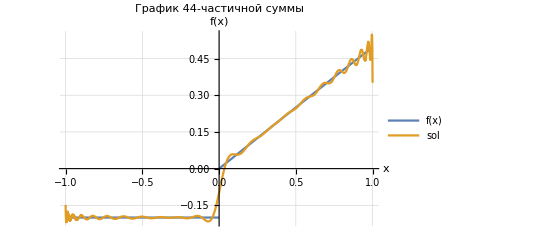

```mathematica
Plot[{f[x],sol},{x,-1,1},PlotRange->All, GridLines->Automatic,PlotLegends->"Expressions",AxesLabel->{"x","f(x)"},PlotLabel->"График 44-частичной суммы"]
```

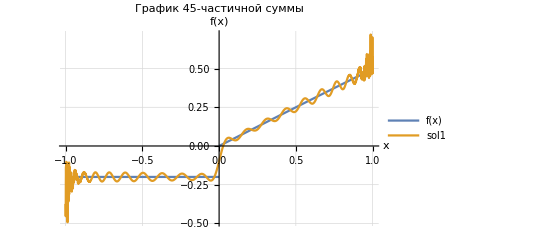

```mathematica
Plot[{f[x],sol1},{x,-1,1},PlotRange->All, GridLines->Automatic,PlotLegends->"Expressions",AxesLabel->{"x","f(x)"},PlotLabel->"График 45-частичной суммы"]
```

Таким образом, n - оптимальное = 44, также стоит отметить особенность данной функции, она имеет разрыв в точке x = 0. Из-за этого в окрестности этой точки сложно добиться наилучшего приближения. Для реализации поставленной задачи (нахождения оптимального n), произведен отступ от точки 0 на 0.01 в обе стороны. Если отступать на большее значение равное 0.05 , то оптимальное n = 11.

```mathematica
sol2=fun[11];
```

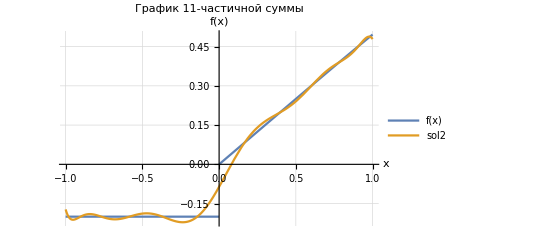

```mathematica
Plot[{f[x],sol2},{x,-1,1},PlotRange->All, GridLines->Automatic,PlotLegends->"Expressions",AxesLabel->{"x","f(x)"},PlotLabel->"График 11-частичной суммы"]
```

Пункт 2
	Разложить данную функцию в ряд по присоединенным полиномам Лежандра второго порядка для x ∈ [−1, 1] , построить на одном графике предложенную функцию и ее n-частичные суммы с n=1,2,…,5,… . Подобрать такое n-оптимальное ,что бы максимальное отклонение n-частичные суммы от данной функции не превышало ϵ = 10% от |sup[f(x)]-inf[f(x)]| для любого x ∈  [−1, 1].

Рассмотрим случай при m = 2

```mathematica
m=2;
cnm[n_,m_]:=(2 n +1)/2*((n-m)!)/((n+m)!)*NIntegrate[f[x]*LegendreP[n,m,x],{x,-1,1}];
funMN[p_]:=Sum[cnm[n,m]*LegendreP[n,m,x],{n,m,p}];
```

Определим оптимальное количество n

```mathematica
iter = 2;
current = Max[Maximize[{funMN[iter]-f[x],-1<x<-0.01},x][[1]],Maximize[{funMN[iter]-f[x],0.01<x<1},x][[1]]];
While[current>error,
iter+=1;
current = Max[MaxValue[{funMN[iter]-f[x], -1<x<-0.01},x],MaxValue[{funMN[iter]-f[x], 0.01<x<1},x]];
Print["n = ", iter, ". Максимальное отклонение при заданном n = ", current];
If[iter ==36,Break[]]
];
```

n = 3. Максимальное отклонение при заданном n =  = 0.2

n = 4. Максимальное отклонение при заданном n =  = 0.2

n = 5. Максимальное отклонение при заданном n =  = 0.2

n = 6. Максимальное отклонение при заданном n =  = 0.2

n = 7. Максимальное отклонение при заданном n =  = 0.2

n = 8. Максимальное отклонение при заданном n =  = 0.2

n = 9. Максимальное отклонение при заданном n =  = 0.2

n = 10. Максимальное отклонение при заданном n =  = 0.2

n = 11. Максимальное отклонение при заданном n =  = 0.2

n = 12. Максимальное отклонение при заданном n =  = 0.2

n = 13. Максимальное отклонение при заданном n =  = 0.2

n = 14. Максимальное отклонение при заданном n =  = 0.2

n = 15. Максимальное отклонение при заданном n =  = 0.2

n = 16. Максимальное отклонение при заданном n =  = 0.2

n = 17. Максимальное отклонение при заданном n =  = 0.0932319

n = 18. Максимальное отклонение при заданном n =  = 0.2

n = 19. Максимальное отклонение при заданном n =  = 0.2

n = 20. Максимальное отклонение при заданном n =  = 0.2

n = 21. Максимальное отклонение при заданном n =  = 0.2

n = 22. Максимальное отклонение при заданном n =  = 0.2

n = 23. Максимальное отклонение при заданном n =  = 0.2

n = 24. Максимальное отклонение при заданном n =  = 0.0855945

n = 25. Максимальное отклонение при заданном n =  = 0.0865071

n = 26. Максимальное отклонение при заданном n =  = 0.089417

n = 27. Максимальное отклонение при заданном n =  = 0.2

n = 28. Максимальное отклонение при заданном n =  = 0.0826957

n = 29. Максимальное отклонение при заданном n =  = 0.2

n = 30. Максимальное отклонение при заданном n =  = 0.0858056

n = 31. Максимальное отклонение при заданном n =  = 0.0826031

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.933578}. NIntegrate obtained 0.662321 and 7.84579×10^-7 for the integral and error estimates.

n = 32. Максимальное отклонение при заданном n =  = 0.079894

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.933578}. NIntegrate obtained 0.662321 and 7.84579×10^-7 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

n = 33. Максимальное отклонение при заданном n =  = 0.0805256

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

n = 34. Максимальное отклонение при заданном n =  = 0.08247

n = 35. Максимальное отклонение при заданном n =  = 0.2

n = 36. Максимальное отклонение при заданном n =  = 0.0771662

```mathematica
sol3=funMN[36];
```

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.933578}. NIntegrate obtained 0.662321 and 7.84579×10^-7 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.908188}. NIntegrate obtained 0.466634 and 1.25981×10^-6 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {0.892563}. NIntegrate obtained 0.523683 and 2.01752×10^-6 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

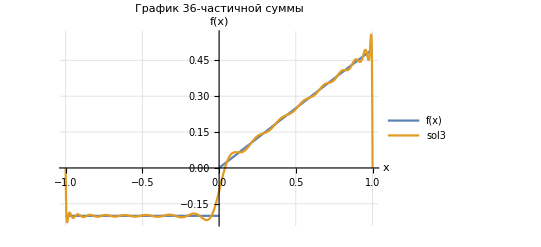

```mathematica
Plot[{f[x],sol3},{x,-1,1},PlotRange->All, GridLines->Automatic,PlotLegends->"Expressions",AxesLabel->{"x","f(x)"},PlotLabel->"График 36-частичной суммы"]
```

Таким образом, при реализации итерационного процесса для нахождения оптимального n, можно заметить, что при n = 36 получается наименьшая погрешность. Для реализации поставленной задачи также (нахождения оптимального n), произведен отступ от точки 0 на 0.01 в обе стороны. Если отступать на большее значение равное 0.05 , то оптимальное n = 17.

```mathematica
sol4=funMN[17];
```

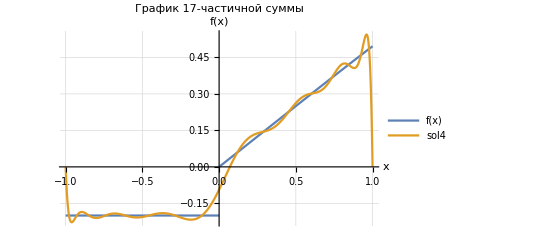

```mathematica
Plot[{f[x],sol4},{x,-1,1},PlotRange->All, GridLines->Automatic,PlotLegends->"Expressions",AxesLabel->{"x","f(x)"},PlotLabel->"График 17-частичной суммы"]
```

Присоединенные полиномы Лежандра второго порядка в точках x = +-1 равны нулю. Что как раз можно наблюдать на графиках выше, при разложении.

Пункт 3
	Разложить данную функцию в ряд по полиномам Эрмита для x ∈ [−1, 1] , построить на одном графике предложенную функцию и ее n-частичные суммы с n=1, 2,…,5,… . Подобрать такое n-оптимальное ,чтобы максимальное отклонение n-частичные суммы от данной функции не превышало ϵ = 10% от |sup[f(x)]-inf[f(x)]| для любого x ∈ [−1, 1].

```mathematica
aH[n_]:=1/(√π n!2^n)*NIntegrate[f[x]*Exp[-x^2]*HermiteH[n,x],{x,-Infinity,Infinity}];
funH[m_]:= Sum[aH[n]*HermiteH[n,x], {n,0, m}];
```

Определим оптимальное количество n

```mathematica
iter=1;
current=Max[Maximize[{funH[iter]-f[x],-1<x<-0.01},x][[1]],Maximize[{funH[iter]-f[x],0.01<x<1},x][[1]]];
While[current>error,iter+=20;
current=Max[MaxValue[{funH[iter]-f[x],-1<x<-0.01},x],MaxValue[{funH[iter]-f[x],0.01<x<1},x]];
Print["n = ",iter,". Максимальное отклонение при заданном n = ",current];
If[iter ==201,Break[]]
];
```

n = 21. Максимальное отклонение при заданном n =  = 0.109461

n = 41. Максимальное отклонение при заданном n =  = 0.115841

n = 61. Максимальное отклонение при заданном n =  = 0.1042

n = 81. Максимальное отклонение при заданном n =  = 0.0978634

n = 101. Максимальное отклонение при заданном n =  = 0.101392

n = 121. Максимальное отклонение при заданном n =  = 0.10171

n = 201. Максимальное отклонение при заданном n =  = 0.102378

n = 141. Максимальное отклонение при заданном n =  = 0.0972113

General::munfl: (1.2178×10^159)/(214284799975031395271568«277»0000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (2.13495×10^161)/(677139967921099209058155«279»0000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::munfl: (4.8441×10^161)/(215330509798909548480493«282»0000000000000000000000000) is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

n = 161. Максимальное отклонение при заданном n =  = 0.102378

n = 181. Максимальное отклонение при заданном n =  = 0.102378

```mathematica
sol5=funH[141];
```

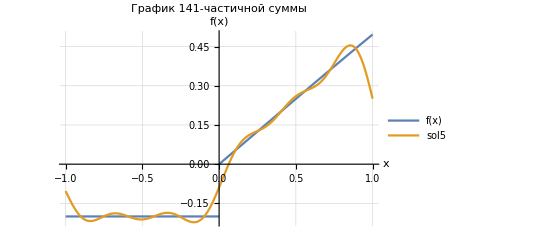

```mathematica
Plot[{f[x],sol5},{x,-1,1},PlotRange->All, GridLines->Automatic,PlotLegends->"Expressions",AxesLabel->{"x","f(x)"},PlotLabel->"График 141-частичной суммы"]
```

```mathematica
sol6=funH[81];
```

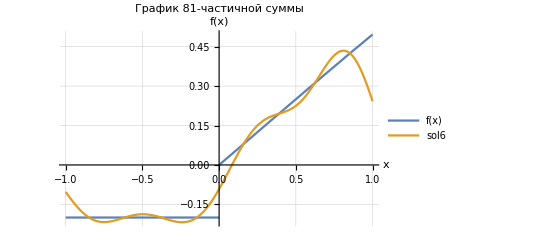

```mathematica
Plot[{f[x],sol6},{x,-1,1},PlotRange->All, GridLines->Automatic,PlotLegends->"Expressions",AxesLabel->{"x","f(x)"},PlotLabel->"График 81-частичной суммы"]
```

Таким образом,  при реализации итерационного процесса для нахождения оптимального n, можно заметить, что начиная с n = 141 значение погрешности не изменяется. Для реализации поставленной задачи также (нахождения оптимального n), произведен отступ от точки 0 на 0.01 в обе стороны. Если отступать на большее значение равное 0.05 , то оптимальное n = 81.

Вывод
	В ходе выполнения лабораторной работы была разложена предложенная функция в ряд по полиномам Лежандра, присоединенным полиномам Лежандра, по полиномам Эрмита на интервале  от -1 до 1. Стоит отметить особенность исходной функции, она имеет разрыв в точке x = 0.
	1) В первом задании  из-за этого нет возможности достигнуть заданного уровня погрешности. Чтобы исправить это,  от x = 0 отступили на 0.01 вправо и влево. Таким образом, n-оптимальное = 44.
	2) Во втором задании также отступили от точки 0 на на 0.01 вправо и влево. Таким образом, n-оптимальное = 36.
	3) В третьем задании произведен тот же отступ от точки 0. Оптимальное n в данном случае равняется 141.
	Если не производить отступ то, чтобы увеличить n до оптимального не хватает вычислительных мощностей ПК.  
	Если сравнивать все три разложения, наиболее точное приближение к функции дало разложение по полиномам Лежандра. Менее точным приближением к заданной функции является разложении по полиномам Эрмита, так как в этом случае погрешность максимальна. 
	Во время выполнения работы были изучены новые функции: NIntegrate[], HermiteH[], LegendreP[].